# S-Curve

```mathematica
Clear[k0,ϵ]
x[k2_] = (z*k2-k0*Cos[θ1])/2+√((z*k2-k0*Cos[θ1])^2/4-k2^2+k0*k2*Cos[θ2]+m*ϵ); (*k2 dependence of k1*)
```

#### Find parameters: a, b, x0, y0

```mathematica
Clear[x0,y0,k0,m,ϵ]
Solve[{2*(x0-y0*(b^2-a^2)/(a^2+b^2))==k0*Cos[θ1],
	2*(-(b^2-a^2)/(a^2+b^2)*x0+y0)==k0*Cos[θ2],
	-2*(b^2-a^2)/(a^2+b^2)==z,
	-2*x0*y0*(b^2-a^2)/(a^2+b^2)+x0^2+y0^2-(2 a^2 b^2)/(a^2+b^2)==-m*ϵ},
	{a, b, x0, y0}]
```

{{a→-(√2 √(4 m ϵ-m z^2 ϵ+k0^2 Cos[θ1]^2-k0^2 z Cos[θ1] Cos[θ2]+k0^2 Cos[θ2]^2))/(√(8-4 z-2 z^2+z^3)),b→-(√2 √(-4 m ϵ+m z^2 ϵ-k0^2 Cos[θ1]^2+k0^2 z Cos[θ1] Cos[θ2]-k0^2 Cos[θ2]^2))/(√(-8-4 z+2 z^2+z^3)),x0→(-2 k0 Cos[θ1]+k0 z Cos[θ2])/(-4+z^2),y0→(k0 (z Cos[θ1]-2 Cos[θ2]))/(-4+z^2)},{a→-(√2 √(4 m ϵ-m z^2 ϵ+k0^2 Cos[θ1]^2-k0^2 z Cos[θ1] Cos[θ2]+k0^2 Cos[θ2]^2))/(√(8-4 z-2 z^2+z^3)),b→(√2 √(-4 m ϵ+m z^2 ϵ-k0^2 Cos[θ1]^2+k0^2 z Cos[θ1] Cos[θ2]-k0^2 Cos[θ2]^2))/(√(-8-4 z+2 z^2+z^3)),x0→(-2 k0 Cos[θ1]+k0 z Cos[θ2])/(-4+z^2),y0→(k0 (z Cos[θ1]-2 Cos[θ2]))/(-4+z^2)},{a→(√2 √(4 m ϵ-m z^2 ϵ+k0^2 Cos[θ1]^2-k0^2 z Cos[θ1] Cos[θ2]+k0^2 Cos[θ2]^2))/(√(8-4 z-2 z^2+z^3)),b→-(√2 √(-4 m ϵ+m z^2 ϵ-k0^2 Cos[θ1]^2+k0^2 z Cos[θ1] Cos[θ2]-k0^2 Cos[θ2]^2))/(√(-8-4 z+2 z^2+z^3)),x0→(-2 k0 Cos[θ1]+k0 z Cos[θ2])/(-4+z^2),y0→(k0 (z Cos[θ1]-2 Cos[θ2]))/(-4+z^2)},{a→(√2 √(4 m ϵ-m z^2 ϵ+k0^2 Cos[θ1]^2-k0^2 z Cos[θ1] Cos[θ2]+k0^2 Cos[θ2]^2))/(√(8-4 z-2 z^2+z^3)),b→(√2 √(-4 m ϵ+m z^2 ϵ-k0^2 Cos[θ1]^2+k0^2 z Cos[θ1] Cos[θ2]-k0^2 Cos[θ2]^2))/(√(-8-4 z+2 z^2+z^3)),x0→(-2 k0 Cos[θ1]+k0 z Cos[θ2])/(-4+z^2),y0→(k0 (z Cos[θ1]-2 Cos[θ2]))/(-4+z^2)}}

```mathematica
Solve[(a Cos[t]+3 b Sin[t])/√2 + x0 + y0 - k0 == 0, t]
```

{{t→ConditionalExpression[ArcTan[(√2 a k0-√2 a x0-√2 a y0-√(9 a^2 b^2+81 b^4-18 b^2 k0^2+36 b^2 k0 x0-18 b^2 x0^2+36 b^2 k0 y0-36 b^2 x0 y0-18 b^2 y0^2))/(a^2+9 b^2),-(-2 k0+(2 a^2 k0)/(a^2+9 b^2)+2 x0-(2 a^2 x0)/(a^2+9 b^2)+2 y0-(2 a^2 y0)/(a^2+9 b^2)-(√2 a √(9 a^2 b^2+81 b^4-18 b^2 k0^2+36 b^2 k0 x0-18 b^2 x0^2+36 b^2 k0 y0-36 b^2 x0 y0-18 b^2 y0^2))/(a^2+9 b^2))/(3 √2 b)]+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[(√2 a k0-√2 a x0-√2 a y0+√(9 a^2 b^2+81 b^4-18 b^2 k0^2+36 b^2 k0 x0-18 b^2 x0^2+36 b^2 k0 y0-36 b^2 x0 y0-18 b^2 y0^2))/(a^2+9 b^2),-(-2 k0+(2 a^2 k0)/(a^2+9 b^2)+2 x0-(2 a^2 x0)/(a^2+9 b^2)+2 y0-(2 a^2 y0)/(a^2+9 b^2)+(√2 a √(9 a^2 b^2+81 b^4-18 b^2 k0^2+36 b^2 k0 x0-18 b^2 x0^2+36 b^2 k0 y0-36 b^2 x0 y0-18 b^2 y0^2))/(a^2+9 b^2))/(3 √2 b)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
ϵ=-0.18;
k0=1;
z[θ1_,θ2_,ϕ_]=Cos[ϕ]Sin[θ1]Sin[θ2]+Cos[θ1]Cos[θ2];
b[θ1_,θ2_,ϕ_]=√((2 ϵ (z[θ1,θ2,ϕ]^2-4)-2 k0^2 (Cos[θ1]^2+Cos[θ2]^2-z[θ1,θ2,ϕ] Cos[θ1]Cos[θ2]))/(z[θ1,θ2,ϕ]^3+2 z[θ1,θ2,ϕ]^2 -4 z[θ1,θ2,ϕ]-8));
a[θ1_,θ2_,ϕ_]=√((2 ϵ (4-z[θ1,θ2,ϕ]^2)+2 k0^2 (Cos[θ1]^2+Cos[θ2]^2-z[θ1,θ2,ϕ] Cos[θ1]Cos[θ2]))/(z[θ1,θ2,ϕ]^3-2 z[θ1,θ2,ϕ]^2 -4 z[θ1,θ2,ϕ]+8));
x0[θ1_,θ2_,ϕ_]=k0 (z[θ1,θ2,ϕ] Cos[θ2]-2 Cos[θ1])/(z[θ1,θ2,ϕ]^2-4);
y0[θ1_,θ2_,ϕ_]=k0 (z[θ1,θ2,ϕ] Cos[θ1]-2 Cos[θ2])/(z[θ1,θ2,ϕ]^2-4);
c[θ1_,θ2_,ϕ_]=(1/a[θ1,θ2,ϕ]^2+1/b[θ1,θ2,ϕ]^2);
d[θ1_,θ2_,ϕ_]=(1/a[θ1,θ2,ϕ]^2-1/b[θ1,θ2,ϕ]^2);
Manipulate[{
ContourPlot[{(*(k1-x0[θ1,θ2,ϕ])^2/a[θ1,θ2,ϕ]+(k2-y0[θ1,θ2,ϕ])^2/b[θ1,θ2,ϕ]==1,*)
k1^2+k2^2-k0*(k1*Cos[θ1]+k2*Cos[θ2])+k1*k2*(Cos[ϕ]*Sin[θ2]*Sin[θ1]+Cos[θ1]*Cos[θ2])==ϵ,
k1^2 c[θ1,θ2,ϕ]/2+k2^2 c[θ1,θ2,ϕ]/2-k1 k2 d[θ1,θ2,ϕ]-k1(c[θ1,θ2,ϕ] x0[θ1,θ2,ϕ]-d[θ1,θ2,ϕ] y0[θ1,θ2,ϕ])-k2(-d[θ1,θ2,ϕ]x0[θ1,θ2,ϕ]+c[θ1,θ2,ϕ] y0[θ1,θ2,ϕ])-d[θ1,θ2,ϕ] x0[θ1,θ2,ϕ] y0[θ1,θ2,ϕ]+c[θ1,θ2,ϕ] (x0[θ1,θ2,ϕ]^2+y0[θ1,θ2,ϕ]^2)/2==1},
			{k1,-5,5},{k2,-5,5},
			Epilog->{PointSize[Medium],Point[{x0[θ1,θ2,ϕ],y0[θ1,θ2,ϕ]}]},
			Axes->True,
			AxesOrigin->{0,0},
			AxesStyle->Black,
			PlotLegends->{(*"shifted",*)"solution","+rotated"}],
ParametricPlot[{(a[θ1,θ2,ϕ]Cos[t]+b[θ1,θ2,ϕ]Sin[t])/√2+x0[θ1,θ2,ϕ],(-a[θ1,θ2,ϕ]Cos[t]+b[θ1,θ2,ϕ]Sin[t])/√2+y0[θ1,θ2,ϕ]},{t,-π/2,5/4 π}]
},
{{θ1,15*π/180},0,π},
{{θ2,15*π/180},0,π},
{{ϕ,π/2},0,2*π}
]
```

```mathematica
ϵ=2;
k0=3;
z[θ1_,θ2_,ϕ_]=Cos[ϕ]Sin[θ1]Sin[θ2]+Cos[θ1]Cos[θ2];
a[θ1_,θ2_,ϕ_]=(2 ϵ (4-z[θ1,θ2,ϕ]^2)+2 k0^2 (Cos[θ1]^2+Cos[θ2]^2+z[θ1,θ2,ϕ] Cos[θ1]Cos[θ2]))/((z[θ1,θ2,ϕ]+2) (z[θ1,θ2,ϕ]-2)^2);
b[θ1_,θ2_,ϕ_]=(2 ϵ (z[θ1,θ2,ϕ]^2-4)-2 k0^2 (Cos[θ1]^2+Cos[θ2]^2+z[θ1,θ2,ϕ] Cos[θ1]Cos[θ2]))/((z[θ1,θ2,ϕ]+2)^2 (z[θ1,θ2,ϕ]-2));
x0[θ1_,θ2_,ϕ_]=-k0 (z[θ1,θ2,ϕ] Cos[θ2]+2 Cos[θ1])/(z[θ1,θ2,ϕ]^2-4);
y0[θ1_,θ2_,ϕ_]=-k0 (z[θ1,θ2,ϕ] Cos[θ1]+2 Cos[θ2])/(z[θ1,θ2,ϕ]^2-4);
c[θ1_,θ2_,ϕ_]=(1/a[θ1,θ2,ϕ]+1/b[θ1,θ2,ϕ]);
d[θ1_,θ2_,ϕ_]=(1/b[θ1,θ2,ϕ]-1/a[θ1,θ2,ϕ]);
Manipulate[{
ContourPlot[{(*(k1-x0[θ1,θ2,ϕ])^2/a[θ1,θ2,ϕ]+(k2-y0[θ1,θ2,ϕ])^2/b[θ1,θ2,ϕ]==1,*)
k1^2+k2^2-k0*(k1*Cos[θ1]+k2*Cos[θ2])+k1*k2*(Cos[ϕ]*Sin[θ2]*Sin[θ1]+Cos[θ1]*Cos[θ2])==ϵ,
k1^2 c[θ1,θ2,ϕ]/2+k2^2 c[θ1,θ2,ϕ]/2-k1 k2 d[θ1,θ2,ϕ]-k1(c[θ1,θ2,ϕ] x0[θ1,θ2,ϕ]-d[θ1,θ2,ϕ] y0[θ1,θ2,ϕ])-k2(-d[θ1,θ2,ϕ]x0[θ1,θ2,ϕ]+c[θ1,θ2,ϕ] y0[θ1,θ2,ϕ])-d[θ1,θ2,ϕ] x0[θ1,θ2,ϕ] y0[θ1,θ2,ϕ]+c[θ1,θ2,ϕ] (x0[θ1,θ2,ϕ]^2+y0[θ1,θ2,ϕ]^2)/2==1},
			{k1,-5,5},{k2,-5,5},
			Epilog->{PointSize[Medium],Point[{x0[θ1,θ2,ϕ],y0[θ1,θ2,ϕ]}]},
			Axes->True,
			AxesOrigin->{0,0},
			AxesStyle->Black,
			PlotLegends->{(*"shifted",*)"solution","+rotated"}],
ParametricPlot[{(√a[θ1,θ2,ϕ] Cos[t]+√b[θ1,θ2,ϕ] Sin[t])/√2+x0[θ1,θ2,ϕ],(-√a[θ1,θ2,ϕ]Cos[t]+√b[θ1,θ2,ϕ] Sin[t])/√2+y0[θ1,θ2,ϕ]},{t,0,π}]
},
{{θ1,15*π/180},0,π},
{{θ2,90*π/180},0,π},
{{ϕ,π/2},0,2*π}
]
```

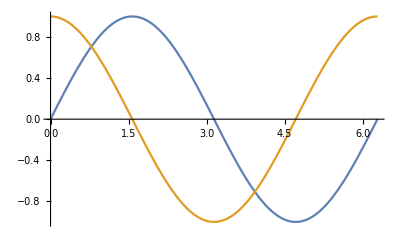

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π}]
```